```mathematica
Quit[]
```

```mathematica
SetDirectory["/Users/saraditsch/Desktop/Wtt/Mathematica"];
```

```mathematica
SetDirectory["/scratch/ge84fet/Wtt/Mathematica/MMatrix"];
```

```mathematica
$LoadAddOns = {"FeynArts"};
Quiet[Check[Get["FeynCalc`"],Print["FeynCalc is not available."]]]
$FAVerbose=0;
FCCheckVersion[9,3,0];
```

FeynCalc 9.3.1 (stable version). For help, use the documentation center, check out the wiki or visit the forum.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 256 (2020) 107478, arXiv:2001.04407.

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 207 (2016) 432-444, arXiv:1601.01167.

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun. 64 (1991) 345-359.

FeynArts 3.11 (25 Mar 2022) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

```mathematica
MakeBoxes[p1,TraditionalForm]:="\!\(\*SubscriptBox[\(p\), \(1\)]\)";
MakeBoxes[p2,TraditionalForm]:="\!\(\*SubscriptBox[\(p\), \(2\)]\)";
MakeBoxes[p3,TraditionalForm]:="\!\(\*SubscriptBox[\(p\), \(3\)]\)";
MakeBoxes[p4,TraditionalForm]:="\!\(\*SubscriptBox[\(p\), \(4\)]\)";
MakeBoxes[p5,TraditionalForm]:="\!\(\*SubscriptBox[\(p\), \(5\)]\)";
```

```mathematica
SetMandelstam[s,{p1,p2,p3,p4,p5},{0,0,SMP["m_t"],SMP["m_t"],SMP["m_W"]}];
Identities={s[1,5] -> 2SMP["m_t"]^2+SMP["m_W"]^2-s[1,2]-s[1,3]-s[1,4], s[2,5]-> 2SMP["m_t"]^2+SMP["m_W"]^2-s[1,2]-s[2,3]-s[2,4], s[3,5]-> 3SMP["m_t"]^2+SMP["m_W"]^2-s[1,3]-s[2,3]-s[3,4], s[4,5]-> 3SMP["m_t"]^2+SMP["m_W"]^2-s[1,4]-s[2,4]-s[3,4]}/.s[3,4]->-(s[2,4]+s[2,3]+s[1,4]+s[1,3]+s[1,2]-4*SMP["m_t"]^2-SMP["m_W"]^2);
AppendTo[Identities,s[3,4]->-(s[2,4]+s[2,3]+s[1,4]+s[1,3]+s[1,2]-4*SMP["m_t"]^2-SMP["m_W"]^2)];
Massless={SMP["m_d"]->0,SMP["m_u"]->0};
```

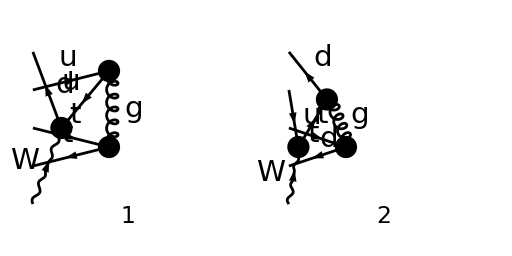

FeynArtsGraphics()(([1] | [2]))

```mathematica
diags=InsertFields[CreateTopologies[0,5->0],{-F[4,{1}],F[3,{1}],F[3,{3}],-F[3,{3}],V[3]}->{},InsertionLevel->{Classes},Model-> "SMQCD",ExcludeParticles->{S[_],V[3],V[1],V[2]}];
Paint[diags,ColumnsXRows->{2,1},Numbering->Simple,SheetHeader->None,ImageSize->{512,256}]
```

```mathematica
diags=InsertFields[CreateTopologies[1,5->0],{-F[4,{1}],F[3,{1}],F[3,{3}],-F[3,{3}],V[3]}->{},InsertionLevel->{Classes},Model-> "SMQCD",ExcludeParticles->{S[_],V[3],V[1],V[2]}];
Paint[diags,ColumnsXRows->{4,1},Numbering->Simple,SheetHeader->None,ImageSize->{512,256}]
```

```mathematica
amp[0]=FCFAConvert[CreateFeynAmp[diags],IncomingMomenta->{p1,p2,p3,p4,p5},OutgoingMomenta->{},ChangeDimension->4,List->False,SMP->True,Contract->True,DropSumOver->True,UndoChiralSplittings->True]//.Massless
```

Part::partw: Part 2 of {} does not exist.

(e g_s^2 T_Col1Col2^Glu6 T_Col4Col3^Glu6 (φ(-OverBar[p_4],m_t)).(γ̄)^Lor2.(φ(OverBar[p_3],m_t)) (φ(-OverBar[p_1])).(γ̄·ε̄(p_5)).(γ̄)^7.(γ̄·(OverBar[p_2]+OverBar[p_3]+OverBar[p_4])).(γ̄)^Lor2.(φ(OverBar[p_2])))/(√2 (sin(θ_W)) (-OverBar[p_3]-OverBar[p_4])^2 (-OverBar[p_2]-OverBar[p_3]-OverBar[p_4])^2)+(e g_s^2 T_Col1Col2^Glu6 T_Col4Col3^Glu6 (φ(-OverBar[p_4],m_t)).(γ̄)^Lor2.(φ(OverBar[p_3],m_t)) (φ(-OverBar[p_1])).(γ̄)^Lor2.(γ̄·(OverBar[p_2]+OverBar[p_5])).(γ̄·ε̄(p_5)).(γ̄)^7.(φ(OverBar[p_2])))/(√2 (sin(θ_W)) (-OverBar[p_2]-OverBar[p_5])^2 (-OverBar[p_3]-OverBar[p_4])^2)

```mathematica
ampSquared[0] = (1/2*1/3)^4*Simplify[(DoPolarizationSums[DiracSimplify[FermionSpinSum[(SUNSimplify[FeynAmpDenominatorExplicit[(1/SUNN^2)*(amp[0]*ComplexConjugate[amp[0]])], Explicit -> True, SUNNToCACF -> False])]], p5] //. Identities)//.Massless]
```

#### Compare Amplitude squared with Max

```mathematica
denumw={den[a_]->1/a};
MaxNotation={mw-> Sqrt[mwsq],mt-> Sqrt[mtsq],gW->gew,D->d};
rewriteCoupl={gs->Sqrt[4 Pi as],gW->Sqrt[4 Sqrt[2]*GF*mwsq]};
plugCoupl={as->0.118,GF->0.000116639};
```

```mathematica
plugMass={mtsq->29998.2,mwsq->6463.84,mzsq->8315.18};
plugKin1={s12->250000.,s13->-38312.6,s14->-111551.,s23->-110709.,s24->-36851.4,s34->173881.};
plugKin2= {s12->250000.,s13->-67762.,s14->-34739.5,s23->-61288.2,s24->-86750.3,s34->126997.};
```

```mathematica
amp=Get["/Users/saraditsch/Desktop/Wtt/TreeLevelAmplitude/TreeLevelAmplitudeSquared.m"];
```

```mathematica
amp//Variables
```

{gs,gW,mt,D,mw,s12,s13,s14,s23,s24,den(2 mt^2+mw^2-s12-s13-s14),den(2 mt^2+mw^2-s12-s23-s24),den(4 mt^2+mw^2-s12-s13-s14-s23-s24)}

```mathematica
(amp//.denumw//.MaxNotation//.rewriteCoupl//.plugCoupl//.plugMass//.plugKin1)/0.10363683192986434
```

-2.12499

```mathematica
(amp//.denumw//.MaxNotation//.rewriteCoupl//.plugCoupl//.plugMass//.plugKin2)/0.05196298888664429
```

-2.12499

```mathematica
Sara=amp//.denumw//.MaxNotation//Together;
```

```mathematica
MaxD1=Get["/Users/saraditsch/Desktop/Wtt/TreeLevelAmplitude/Max/D1.m"];
MaxD2=Get["/Users/saraditsch/Desktop/Wtt/TreeLevelAmplitude/Max/D2.m"];
MaxNicer={diagid[a_]->1,cOlNA->1,cOlI2R->1};
Identities2={s15 -> 2*mt^2+mw^2-s12-s13-s14, s25-> 2mt^2+mw^2-s12-s23-s24, s35-> 3mt^2+mw^2-s13-s23-s34, s45-> 3mt^2+mw^2-s14-s24-s34}/.s34->-(s24+s23+s14+s13+s12-4*mt^2-mw^2);
AppendTo[Identities2,s34->-(s24+s23+s14+s13+s12-4*mt^2-mw^2)];
```

```mathematica
MaxDel=(MaxD1+MaxD2//.MaxNicer//.denumw//.Identities2//.MaxNotation)//Together;
```

```mathematica
Sara/MaxDel//Together
```

-2

#### Factor out gram in numerator of Formfactor?

```mathematica
GRAM=-4*mt^4*mw^2*s12+4*mt^4*s12^2+4*mt^2*mw^2*s12^2+mw^4*s12^2-4*mt^2*s12^3-2*mw^2*s12^3+s12^4+4*mt^4*s12*s13+2*mt^2*mw^2*s12*s13-6*mt^2*s12^2*s13-2*mw^2*s12^2*s13+2*s12^3*s13+mt^4*s13^2-2*mt^2*s12*s13^2+s12^2*s13^2+4*mt^4*s12*s14+2*mt^2*mw^2*s12*s14-6*mt^2*s12^2*s14-2*mw^2*s12^2*s14+2*s12^3*s14-2*mt^4*s13*s14-4*mt^2*s12*s13*s14+2*s12^2*s13*s14+mt^4*s14^2-2*mt^2*s12*s14^2+s12^2*s14^2+4*mt^4*s12*s23+2*mt^2*mw^2*s12*s23-6*mt^2*s12^2*s23-2*mw^2*s12^2*s23+2*s12^3*s23-2*mt^4*s13*s23+2*s12^2*s13*s23+2*mt^4*s14*s23-8*mt^2*s12*s14*s23-2*mw^2*s12*s14*s23+4*s12^2*s14*s23+2*mt^2*s13*s14*s23+2*s12*s13*s14*s23-2*mt^2*s14^2*s23+2*s12*s14^2*s23+mt^4*s23^2-2*mt^2*s12*s23^2+s12^2*s23^2-2*mt^2*s14*s23^2+2*s12*s14*s23^2+s14^2*s23^2+4*mt^4*s12*s24+2*mt^2*mw^2*s12*s24-6*mt^2*s12^2*s24-2*mw^2*s12^2*s24+2*s12^3*s24+2*mt^4*s13*s24-8*mt^2*s12*s13*s24-2*mw^2*s12*s13*s24+4*s12^2*s13*s24-2*mt^2*s13^2*s24+2*s12*s13^2*s24-2*mt^4*s14*s24+2*s12^2*s14*s24+2*mt^2*s13*s14*s24+2*s12*s13*s14*s24-2*mt^4*s23*s24-4*mt^2*s12*s23*s24+2*s12^2*s23*s24+2*mt^2*s13*s23*s24+2*s12*s13*s23*s24+2*mt^2*s14*s23*s24+2*s12*s14*s23*s24-2*s13*s14*s23*s24+mt^4*s24^2-2*mt^2*s12*s24^2+s12^2*s24^2-2*mt^2*s13*s24^2+2*s12*s13*s24^2+s13^2*s24^2;
```

```mathematica
F1=Get["/Users/saraditsch/Desktop/Wtt/TreeLevelAmplitude/Formfactors/Formfactor1.m"];
```

```mathematica
nums=Union[Cases[F1,_num,{0,Infinity}]]//.{num[a__]->a}
```

{mt,4 s12^2 mt^4+s13^2 mt^4+s14^2 mt^4+s23^2 mt^4+s24^2 mt^4-4 mw^2 s12 mt^4+4 s12 s13 mt^4+4 s12 s14 mt^4-2 s13 s14 mt^4+4 s12 s23 mt^4-2 s13 s23 mt^4+2 s14 s23 mt^4+4 s12 s24 mt^4+2 s13 s24 mt^4-2 s14 s24 mt^4-2 s23 s24 mt^4-4 s12^3 mt^2+4 mw^2 s12^2 mt^2-2 s12 s13^2 mt^2-2 s12 s14^2 mt^2-2 s12 s23^2 mt^2-2 s14 s23^2 mt^2-2 s12 s24^2 mt^2-2 s13 s24^2 mt^2-6 s12^2 s13 mt^2+2 mw^2 s12 s13 mt^2-6 s12^2 s14 mt^2+2 mw^2 s12 s14 mt^2-4 s12 s13 s14 mt^2-6 s12^2 s23 mt^2-2 s14^2 s23 mt^2+2 mw^2 s12 s23 mt^2-8 s12 s14 s23 mt^2+2 s13 s14 s23 mt^2-6 s12^2 s24 mt^2-2 s13^2 s24 mt^2+2 mw^2 s12 s24 mt^2-8 s12 s13 s24 mt^2+2 s13 s14 s24 mt^2-4 s12 s23 s24 mt^2+2 s13 s23 s24 mt^2+2 s14 s23 s24 mt^2+s12^4-2 mw^2 s12^3+mw^4 s12^2+s12^2 s13^2+s12^2 s14^2+s12^2 s23^2+s14^2 s23^2+2 s12 s14 s23^2+s12^2 s24^2+s13^2 s24^2+2 s12 s13 s24^2+2 s12^3 s13-2 mw^2 s12^2 s13+2 s12^3 s14-2 mw^2 s12^2 s14+2 s12^2 s13 s14+2 s12^3 s23-2 mw^2 s12^2 s23+2 s12 s14^2 s23+2 s12^2 s13 s23+4 s12^2 s14 s23-2 mw^2 s12 s14 s23+2 s12 s13 s14 s23+2 s12^3 s24-2 mw^2 s12^2 s24+2 s12 s13^2 s24+4 s12^2 s13 s24-2 mw^2 s12 s13 s24+2 s12^2 s14 s24+2 s12 s13 s14 s24+2 s12^2 s23 s24+2 s12 s13 s23 s24+2 s12 s14 s23 s24-2 s13 s14 s23 s24,-16 mt^8-8 mw^2 mt^6+24 s12 mt^6+8 s13 mt^6+16 s14 mt^6+16 s23 mt^6+24 s24 mt^6-12 s12^2 mt^4-2 s13^2 mt^4-2 s14^2 mt^4-6 s23^2 mt^4-10 s24^2 mt^4+12 mw^2 s12 mt^4+2 mw^2 s13 mt^4-14 s12 s13 mt^4+6 mw^2 s14 mt^4-18 s12 s14 mt^4-4 s13 s14 mt^4+6 mw^2 s23 mt^4-18 s12 s23 mt^4-4 s13 s23 mt^4-16 s14 s23 mt^4+10 mw^2 s24 mt^4-22 s12 s24 mt^4-12 s13 s24 mt^4-24 s14 s24 mt^4-16 s23 s24 mt^4+2 s12^3 mt^2+s23^3 mt^2+s24^3 mt^2-4 mw^2 s12^2 mt^2+3 s12 s13^2 mt^2+3 s12 s14^2 mt^2-mw^2 s23^2 mt^2+6 s12 s23^2 mt^2+6 s14 s23^2 mt^2-3 mw^2 s24^2 mt^2+4 s12 s24^2 mt^2+4 s13 s24^2 mt^2+10 s14 s24^2 mt^2+3 s23 s24^2 mt^2+2 mw^4 s12 mt^2+7 s12^2 s13 mt^2-3 mw^2 s12 s13 mt^2+7 s12^2 s14 mt^2-3 mw^2 s12 s14 mt^2+6 s12 s13 s14 mt^2+5 s12^2 s23 mt^2+s13^2 s23 mt^2+s14^2 s23 mt^2-9 mw^2 s12 s23 mt^2-mw^2 s13 s23 mt^2+5 s12 s13 s23 mt^2-5 mw^2 s14 s23 mt^2+9 s12 s14 s23 mt^2+2 s13 s14 s23 mt^2+5 s12^2 s24 mt^2+3 s13^2 s24 mt^2+3 s14^2 s24 mt^2+3 s23^2 s24 mt^2-9 mw^2 s12 s24 mt^2-3 mw^2 s13 s24 mt^2+11 s12 s13 s24 mt^2-7 mw^2 s14 s24 mt^2+15 s12 s14 s24 mt^2+6 s13 s14 s24 mt^2-4 mw^2 s23 s24 mt^2+10 s12 s23 s24 mt^2+4 s13 s23 s24 mt^2+16 s14 s23 s24 mt^2-s12 s23^3-s14 s23^3-s14 s24^3-s12^2 s13^2-s12^2 s14^2-s12^2 s23^2+2 mw^2 s12 s23^2+mw^2 s14 s23^2-s12 s14 s23^2-s13^2 s24^2-s14^2 s24^2+mw^2 s12 s24^2+mw^2 s13 s24^2-s12 s13 s24^2+2 mw^2 s14 s24^2-2 s12 s14 s24^2-2 s13 s14 s24^2-s12 s23 s24^2-3 s14 s23 s24^2-s12^3 s13+mw^2 s12^2 s13-s12^3 s14+mw^2 s12^2 s14-2 s12^2 s13 s14+mw^2 s12^2 s23-s12 s13^2 s23-s12 s14^2 s23-mw^4 s12 s23-s12^2 s13 s23+mw^2 s12 s13 s23-s12^2 s14 s23+mw^2 s12 s14 s23-2 s12 s13 s14 s23+mw^2 s12^2 s24-2 s12 s13^2 s24-2 s12 s14^2 s24-2 s12 s23^2 s24-3 s14 s23^2 s24-mw^4 s12 s24-2 s12^2 s13 s24+2 mw^2 s12 s13 s24-2 s12^2 s14 s24+2 mw^2 s12 s14 s24-4 s12 s13 s14 s24-s12^2 s23 s24-s13^2 s23 s24-s14^2 s23 s24+3 mw^2 s12 s23 s24+mw^2 s13 s23 s24-s12 s13 s23 s24+3 mw^2 s14 s23 s24-3 s12 s14 s23 s24-2 s13 s14 s23 s24}

```mathematica
nums[[2]] -GRAM//Simplify
```

0

```mathematica
nums[[2]]-(mt^4*s23^2-2*mt^4*s24*s23+mt^4*s24^2-2*s12*mt^2*s23^2
-4*s12*mt^2*s24*s23-2*s12*mt^2*s24^2+4*s12*mt^4*s23+4*s12*mt^4*s24+2*s12*mw^2*mt^2*s23+2*s12*mw^2*mt^2*s24-4*s12*mw^2*mt^4+s12^2*s23^2+2*s12^2*s24*s23+s12^2*s24^2-6*s12^2*mt^2*s23-6*s12^2*mt^2*s24+4*s12^2*mt^4-2*s12^2*mw^2*s23-2*s12^2*mw^2*s24+4*s12^2*mw^2*mt^2+s12^2*mw^4+2*s12^3*s23+2*s12^3*s24-4*s12^3*mt^2-2*s12^3*mw^2+s12^4+2*s13*mt^2*s24*s23-2*s13*mt^2*s24^2-2*s13*mt^4*s23+2*s13*mt^4*s24+2*s13*s12*s24*s23+2*s13*s12*s24^2-8*s13*s12*mt^2*s24+4*s13*s12*mt^4-2*s13*s12*mw^2*s24+2*s13*s12*mw^2*mt^2+2*s13*s12^2*s23+4*s13*s12^2*s24-6*s13*s12^2*mt^2-2*s13*s12^2*mw^2+2*s13*s12^3+s13^2*s24^2-2*s13^2*mt^2*s24+s13^2*mt^4+2*s13^2*s12*s24-2*s13^2*s12*mt^2+s13^2*s12^2-2*s14*mt^2*s23^2+2*s14*mt^2*s24*s23+2*s14*mt^4*s23-2*s14*mt^4*s24+2*s14*s12*s23^2+2*s14*s12*s24*s23-8*s14*s12*mt^2*s23+4*s14*s12*mt^4-2*s14*s12*mw^2*s23+2*s14*s12*mw^2*mt^2+4*s14*s12^2*s23+2*s14*s12^2*s24-6*s14*s12^2*mt^2-2*s14*s12^2*mw^2+2*s14*s12^3-2*s14*s13*s24*s23+2*s14*s13*mt^2*s23+2*s14*s13*mt^2*s24-2*s14*s13*mt^4+2*s14*s13*s12*s23+2*s14*s13*s12*s24-4*s14*s13*s12*mt^2+2*s14*s13*s12^2+s14^2*s23^2-2*s14^2*mt^2*s23+s14^2*mt^4+2*s14^2*s12*s23-2*s14^2*s12*mt^2+s14^2*s12^2)
```

0

#### Check Formfactor Combination for Helicity Formfactors

```mathematica
Quiet[Check[Get["FeynCalc`"],Print["FeynCalc is not available."]]]
$FAVerbose=0;
FCCheckVersion[9,3,0];
```

FeynCalc 9.3.1 (stable version). For help, use the documentation center, check out the wiki or visit the forum.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 256 (2020) 107478, arXiv:2001.04407.

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 207 (2016) 432-444, arXiv:1601.01167.

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun. 64 (1991) 345-359.

```mathematica
epsP5=ChangeDimension[Conjugate[PolarizationVector[p5,μ,Transversality-> True]],4];
SpinorP1=SpinorVBar[Momentum[p1,4]];
SpinorP2=SpinorU[Momentum[p2,4]];
SpinorP3=SpinorVBar[Momentum[p3,4],SMP["m_t"]];
SpinorP4=SpinorU[Momentum[p4,4],SMP["m_t"]];
Identities={s[1,5] -> 2SMP["m_t"]^2+SMP["m_W"]^2-s[1,2]-s[1,3]-s[1,4], s[2,5]-> 2SMP["m_t"]^2+SMP["m_W"]^2-s[1,2]-s[2,3]-s[2,4], s[3,5]-> 3SMP["m_t"]^2+SMP["m_W"]^2-s[1,3]-s[2,3]-s[3,4], s[4,5]-> 3SMP["m_t"]^2+SMP["m_W"]^2-s[1,4]-s[2,4]-s[3,4]}/.s[3,4]->-(s[2,4]+s[2,3]+s[1,4]+s[1,3]+s[1,2]-4*SMP["m_t"]^2-SMP["m_W"]^2);
AppendTo[Identities,s[3,4]->-(s[2,4]+s[2,3]+s[1,4]+s[1,3]+s[1,2]-4*SMP["m_t"]^2-SMP["m_W"]^2)];
SetMandelstam[s,{p1,p2,p3,p4,p5},{0,0,SMP["m_t"],SMP["m_t"],SMP["m_W"]}];
PL=DiracGamma[7];
PR=DiracGamma[6];
```

```mathematica
(Math=(SpinorP1.PR.GS[p4].PL.SpinorP2 ComplexConjugate[SpinorP2].PR.GS[p3].PL.ComplexConjugate[SpinorP1]//FermionSpinSum//DiracSimplify)//.Identities)//Factor
```

1/2 (4 ⅈ (ϵ̄)^(OverBar[p1]OverBar[p2]OverBar[p3]OverBar[p4])-2 s(1,2) m_t^2-s(1,3) m_t^2-s(1,4) m_t^2-s(2,3) m_t^2-s(2,4) m_t^2-s(1,2) m_W^2+(s(1,2))^2+s(1,2) s(1,3)+s(1,2) s(1,4)+s(1,2) s(2,3)+s(1,4) s(2,3)+s(1,2) s(2,4)+s(1,3) s(2,4)+2 m_t^4)

```mathematica
Hand = ((1/2*(-I*Eps[Momentum[p1], Momentum[p2], Momentum[p3], Momentum[p4]] + DiracTrace[GS[p1] . GS[p4] . GS[p2] . GS[p3]])//DiracSimplify)//.Identities)//Factor
```

1/2 (-ⅈ (ϵ̄)^(OverBar[p1]OverBar[p2]OverBar[p3]OverBar[p4])-2 s(1,2) m_t^2-s(1,3) m_t^2-s(1,4) m_t^2-s(2,3) m_t^2-s(2,4) m_t^2-s(1,2) m_W^2+(s(1,2))^2+s(1,2) s(1,3)+s(1,2) s(1,4)+s(1,2) s(2,3)+s(1,4) s(2,3)+s(1,2) s(2,4)+s(1,3) s(2,4)+2 m_t^4)

```mathematica
Math-Hand//Together//Simplify
```

5/2 ⅈ (ϵ̄)^(OverBar[p1]OverBar[p2]OverBar[p3]OverBar[p4])

#### Compare direct Amplitude squared with one from Formfactors (Only valid in d=4)

```mathematica
F1=Get["/Users/saraditsch/Desktop/Wtt/TreeLevelAmplitude/Formfactors/Formfactor1.m"];
F2=Get["/Users/saraditsch/Desktop/Wtt/TreeLevelAmplitude/Formfactors/Formfactor2.m"];
F3=Get["/Users/saraditsch/Desktop/Wtt/TreeLevelAmplitude/Formfactors/Formfactor3.m"];
F4=Get["/Users/saraditsch/Desktop/Wtt/TreeLevelAmplitude/Formfactors/Formfactor4.m"];
F5=Get["/Users/saraditsch/Desktop/Wtt/TreeLevelAmplitude/Formfactors/Formfactor5.m"];
F6=Get["/Users/saraditsch/Desktop/Wtt/TreeLevelAmplitude/Formfactors/Formfactor6.m"];F7=Get["/Users/saraditsch/Desktop/Wtt/TreeLevelAmplitude/Formfactors/Formfactor7.m"];
F8=Get["/Users/saraditsch/Desktop/Wtt/TreeLevelAmplitude/Formfactors/Formfactor8.m"];F9=Get["/Users/saraditsch/Desktop/Wtt/TreeLevelAmplitude/Formfactors/Formfactor9.m"];F10=Get["/Users/saraditsch/Desktop/Wtt/TreeLevelAmplitude/Formfactors/Formfactor10.m"];F11=Get["/Users/saraditsch/Desktop/Wtt/TreeLevelAmplitude/Formfactors/Formfactor11.m"];F12=Get["/Users/saraditsch/Desktop/Wtt/TreeLevelAmplitude/Formfactors/Formfactor12.m"];F13=Get["/Users/saraditsch/Desktop/Wtt/TreeLevelAmplitude/Formfactors/Formfactor13.m"];F14=Get["/Users/saraditsch/Desktop/Wtt/TreeLevelAmplitude/Formfactors/Formfactor14.m"];F15=Get["/Users/saraditsch/Desktop/Wtt/TreeLevelAmplitude/Formfactors/Formfactor15.m"];F16=Get["/Users/saraditsch/Desktop/Wtt/TreeLevelAmplitude/Formfactors/Formfactor16.m"];
F17=Get["/Users/saraditsch/Desktop/Wtt/TreeLevelAmplitude/Formfactors/Formfactor17.m"];
F18=Get["/Users/saraditsch/Desktop/Wtt/TreeLevelAmplitude/Formfactors/Formfactor18.m"];F19=Get["/Users/saraditsch/Desktop/Wtt/TreeLevelAmplitude/Formfactors/Formfactor19.m"];
F20=Get["/Users/saraditsch/Desktop/Wtt/TreeLevelAmplitude/Formfactors/Formfactor20.m"];
F21=Get["/Users/saraditsch/Desktop/Wtt/TreeLevelAmplitude/Formfactors/Formfactor21.m"];
F22=Get["/Users/saraditsch/Desktop/Wtt/TreeLevelAmplitude/Formfactors/Formfactor22.m"];
F23=Get["/Users/saraditsch/Desktop/Wtt/TreeLevelAmplitude/Formfactors/Formfactor23.m"];
F24=Get["/Users/saraditsch/Desktop/Wtt/TreeLevelAmplitude/Formfactors/Formfactor24.m"];
M=Get["/Users/saraditsch/Desktop/Wtt/MMatrix/Mathematica/MMatrix"];
```

```mathematica
amp=Get["/Users/saraditsch/Desktop/Wtt/TreeLevelAmplitude/TreeLevelAmplitudeSquared.m"];
```

```mathematica
F={F1,F2,F3,F4,F5,F6,F7,F8,F9,F10,F11,F12,F13,F14,F15,F16,F17,F18,F19,F20,F21,F22,F23,F24}//.{num[GRAM]->num[gram]};
```

```mathematica
Asqrt=F.M.F;
```

```mathematica
A2=Asqrt//.{imag->I,num[a__]->a,den[a_]->1/a};
```

```mathematica
A4=A2//.{s[1,2]->s12,s[1,3]->s13,s[1,4]->s14,s[2,3]->s23,s[2,4]->s24,SMP["m_t"]->mt,SMP["m_W"]->mw};
```

```mathematica
A5=A4//.{del[ciext3,ciext5]^2->3,del[ciext1,ciext7]^2->3,del[ciext1,ciext3]^2->3,del[ciext5,ciext7]^2->3,del[a_,b_]^2->3,del[a_,b_]*del[b_,c_]->del[a,c]};
```

```mathematica
A6=A5//Expand;
```

```mathematica
A7=A6//.{del[ciext3,ciext5]^2->3,del[ciext1,ciext7]^2->3,del[ciext1,ciext3]^2->3,del[ciext5,ciext7]^2->3,del[a_,b_]^2->d,del[a_,b_]*del[b_,c_]->del[a,c],gram->GRAM};
```

```mathematica
A9=A7//Factor;
```

```mathematica
Amp=amp//.{den[a_]->1/a,D->4};
```

```mathematica
(A9/Amp)//Factor
```

1